```mathematica
SetDirectory[NotebookDirectory[]]
pblue=Lighter[Blue];
pyellow=Lighter[Yellow];
pred=Lighter[Red];
pgreen=Lighter[Green];
cf=Piecewise[{{Blend[{pred,pblue},(#+Pi)/(Pi/2)],#≤-Pi/2},{Blend[{pblue,pgreen},(#+Pi/2)/(Pi/2)],#≤0},{Blend[{pgreen,pyellow},(#)/(Pi/2)],#≤Pi/2},{Blend[{pyellow,pred},(#-Pi/2)/(Pi/2)],#≤Pi}}]&;
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]]
phase[l:{_?NumericQ..}]:=Module[{args=Arg[l]},args+Prepend[2Pi Accumulate@-IntegerPart@Differences[args/Pi],0]]
nmax=10;
getphase[sig_]:=Module[{asig,plst,S1,slst1,f1},
asig=Fourier[ReplacePart[InverseFourier[sig-Mean[sig]],Join[{{1}},{#}&/@(Floor[Length[sig]/2]+Range[Floor[Length[sig]/2]])]->0]];
plst=phase[asig];
S1[n_]:=Sum[Exp[-I*n*plst[[i]]], {i,1,Length[plst]}]/Length[plst];
slst1=Table[S1[n]/(I*n),{n,1,nmax}];
f1[θ_]:=θ+Evaluate[Sum[2*Re[slst1][[n]]*(Cos[n*θ]-1)-2*Im[slst1][[n]]*Sin[n*θ],{n,1,nmax}]];
f1/@plst]
```

/Users/zack/Documents/oscillators/snakingoscillators

#### Single trajectory runs

-Graphics-

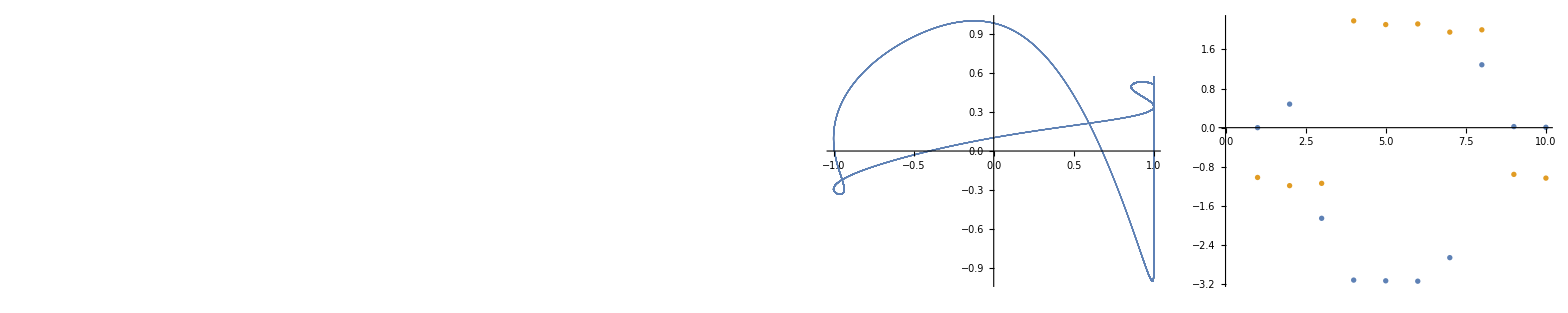

```mathematica
filebase="data/chimeras/1";
dat=BinaryReadList[filebase<>"phases.npy","Real64"][[17;;-1]];
{seed,order,period,norm}=Import[filebase<>"out.dat"][[-1]];
M=10;
theta=ArcTan[Partition[dat,4*M][[All,1;;M]],Partition[dat,4*M][[All,M+1;;2*M]]];
phi=ArcTan[Partition[dat,4*M][[All,2*M+1;;3*M]],Partition[dat,4*M][[All,3*M+1;;4*M]]];
orders=BinaryReadList[filebase<>"order.npy","Real64"][[17;;-1]];
rasterizeBackground[ListPlot[orders,ImageSize->300]]
phases=Transpose[Catenate[{Transpose[theta],Transpose[phi]}]];
dphases=(Mod[#-#[[1]]+Pi,2*Pi]-Pi&/@phases);

If[period>0,
nperiod=Round[period/0.1];
Grid[{{rasterizeBackground[ListDensityPlot[dphases[[1;;nperiod,1;;M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[dphases[[1;;nperiod,M+1;;2*M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],ListPlot[Transpose[{Cos[dphases[[All,2]]],Cos[dphases[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300],ListPlot[{dphases[[-1,1;;M]],dphases[[-1,M+1;;-1]]},ImageSize->300]}}]]
If[Length[periods]>0,{period,Mean[orders[[-period;;-1]]],Norm[Differences[dphases[[-period+1;;-1]]],2]}]
```

```mathematica
Mean[Abs[Total[Transpose[1/(2*M)*(Exp[I*theta[[1;;nperiod]]]+Exp[I*phi[[1;;nperiod]]])]]]^2]^0.5
```

5.51923×10^-16

```mathematica
Mean[Table[Abs[Sum[1/(2*M)*(Exp[I*theta[[n,i]]]+Exp[I*phi[[n,i]]]),{i,1,M}]]^2,{n,1,nperiod}]]^0.5
Mean[Table[Abs[Sum[1/(2*M)*(Exp[I*(theta[[n,i]]+2*Pi/M*(i-1))]+Exp[I*(phi[[n,i]]+2*Pi/M*(i-1))]),{i,1,M}]]^2,{n,1,nperiod}]]^0.5
Mean[Table[Abs[Sum[1/(2*M)*(Exp[I*(theta[[n,i]]-2*Pi/M*(i-1))]+Exp[I*(phi[[n,i]]-2*Pi/M*(i-1))]),{i,1,M}]]^2,{n,1,nperiod}]]^0.5
```

5.49164×10^-16

0.57796

0.458524

```mathematica
rasterizeBackground[ListDensityPlot[theta[[-1000;;-1]]-phi[-1000;;-1]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]
```

$Aborted

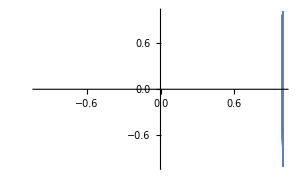

```mathematica
ListPlot[Transpose[{Cos[dphases[[-10000;;-1,2]]],Cos[dphases[[-10000;;-1,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]
```

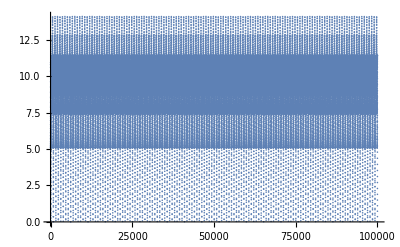

756.718

0.451916

```mathematica
ListPlot[norms]
N[Mean[periods]]
N[StandardDeviation[periods]]
```

```mathematica
-2*Round[period/0.1]
```

-30160

```mathematica
5000/(0.1*period)
```

33.1565

```mathematica
Length[dphases]
```

50000

```mathematica
Norm[Mod[dphases[[-Round[period];;-1]]-dphases[[-10*Round[period];;-9*Round[period]-1]]+Pi,2*Pi]-Pi]
```

35.9069

#### Chimeras from random initial conditions

```mathematica
vals={#[[1]],#[[2]],#[[3]]/300,#[[4]]}&/@SortBy[Import["random.dat"],Norm[#[[2;;4]]]&];
dorder=0.01;
dperiod=0.01;
dnorm=0.01;
{bins,array}=HistogramList[vals[[All,2;;4]],{{dorder*(Range[1/dorder]-1)},{0.1+dperiod*(Range[3/dperiod]-1)},{dnorm*(Range[2/dnorm]-1)}}];
uniq=Table[{i,j,k}=case;
First@Cases[vals,u_/;u[[2]]>=bins[[1,i]]&&u[[2]]<=bins[[1,i+1]]&&u[[3]]>=bins[[2,j]]&&u[[3]]<=bins[[2,j+1]]&&u[[4]]>=bins[[3,k]]&&u[[4]]<=bins[[3,k+1]]],{case,(First/@ArrayRules[array])[[1;;-2]]}];
Length[uniq]
SortBy[{#[[1]],#[[2]],#[[3]]*300,#[[4]]}&/@uniq,{#[[2]],#[[3]],#[[4]]}&]

If[!DirectoryQ["data/chimeras"],CreateDirectory["data/chimeras"]]
seeds=uniq[[All,1]];
Do[CopyFile["data/random/"<>ToString[seeds[[i]]]<>"fs.npy","data/chimeras/"<>ToString[i]<>"ic.npy",OverwriteTarget->True], {i,1,Length[seeds]}]
Last/@ArrayRules[array][[1;;-2]]
```

10

{{822,7.86954×10^-16,43.7141,0.237467},{199,0.309889,93.0462,1.62203},{88,0.444722,92.9085,1.10769},{441,0.505823,93.3858,0.480243},{28,0.505863,93.3858,0.479485},{326,0.53729,90.2009,0.273056},{417,0.540555,88.9955,0.275255},{567,0.57116,93.9305,0.164956},{70,0.579997,92.9358,0.597037},{361,0.717616,93.9533,0.0818283}}

{1,1,18,2,1,2,3,63,1,211}

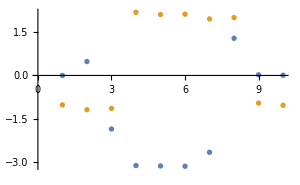
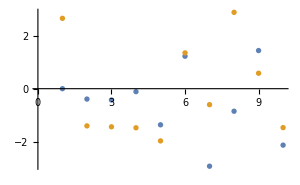
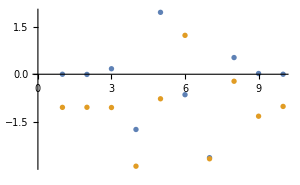
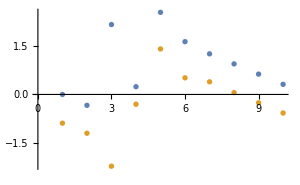
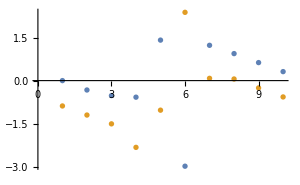
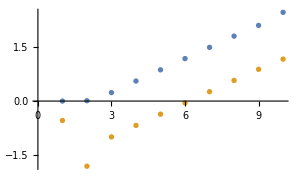
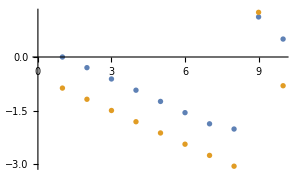
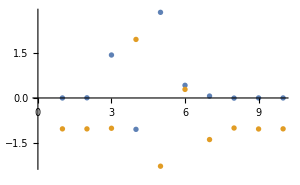
1 | 4.2307×10^-16 | 43.7142 | 0.238113 | 2.42587 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
2 | 0.309914 | 93.0462 | 1.62156 | 24.8733 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
3 | 0.444715 | 92.9096 | 1.10854 | 3.89638 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
4 | 0.505831 | 93.3865 | 0.480094 | 4.12425 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
5 | 0.505873 | 93.3865 | 0.479502 | 3.98015 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
6 | 0.53729 | 90.2019 | 0.27434 | 0.218262 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
7 | 0.540619 | 88.9964 | 0.275104 | 0.689971 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
8 | 0.579997 | 92.9365 | 0.597456 | 12.4475 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
9 | 0.571151 | 93.9308 | 0.165257 | 10.318 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
10 | 0.717596 | 93.9538 | 0.0822271 | 10.9378 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Monitor[p=Grid[DeleteCases[Table[filebase="data/chimeras/"<>ToString[j];
{seed,order,period,norm}=Import[filebase<>"out.dat"][[-1]];
dat=BinaryReadList[filebase<>"phases.npy","Real64"][[17;;-1]];
M=10;
theta=ArcTan[Partition[dat,4*M][[All,1;;M]],Partition[dat,4*M][[All,M+1;;2*M]]];
phi=ArcTan[Partition[dat,4*M][[All,2*M+1;;3*M]],Partition[dat,4*M][[All,3*M+1;;4*M]]];
phases=Transpose[Catenate[{Transpose[theta],Transpose[phi]}]];
phases2=Transpose[Catenate[{-Reverse[Transpose[phi]],-Reverse[Transpose[theta]]}]];
dphases=(Mod[#-#[[1]]+Pi,2*Pi]-Pi&/@phases);
dphases2=(#-#[[1]]&/@phases2);
norms=Norm[Mod[#-dphases[[-1]]+Pi,2*Pi]-Pi]&/@dphases;
mins=First/@Position[Differences[Sign[Differences[norms]]],u_/;u>0];
periods=Differences[Cases[mins,u_/;norms[[u]]<1]];
test=Norm[Mod[dphases[[-Round[period/0.1];;-1]]-dphases[[-10*Round[period/0.1];;-9*Round[period/0.1]-1]]+Pi,2*Pi]-Pi];
If[period>0,
{Grid[{{j,order,period,norm,test,rasterizeBackground[ListDensityPlot[dphases[[1;;Round[period/0.1];;10,1;;M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[dphases[[1;;Round[period/0.1];;10,M+1;;2*M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListPlot[Transpose[{Cos[dphases[[All,2]]],Cos[dphases[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]],rasterizeBackground[ListPlot[Transpose[{Cos[dphases2[[All,2]]],Cos[dphases2[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]],ListPlot[{dphases[[-1,1;;M]],dphases[[-1,M+1;;-1]]},ImageSize->300]}}]}],{j,1,Length[uniq]}],Null]],j]
```

#### Plot auto results

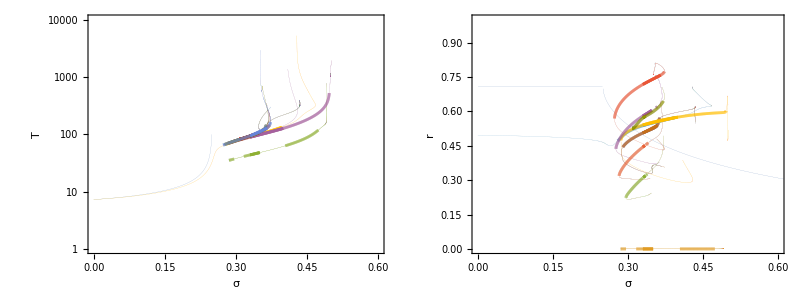

diagram.pdf

```mathematica
M=10;
branches={DeleteCases[Import["auto/rel/steady.dat"],{}]};
stables={DeleteCases[DeleteCases[Import["auto/rel/steady.dat"],{}],u_/;u[[5]]<62]};
Monitor[Do[
If[FileExistsQ["auto/rel/small/"<>ToString[i]<>"fw.dat"]&&FileExistsQ["auto/rel/small/"<>ToString[i]<>"rv.dat"],
branch=Catenate[{Reverse[DeleteCases[Import["auto/rel/small/"<>ToString[i]<>"rv.dat"],{}]],DeleteCases[Import["auto/rel/small/"<>ToString[i]<>"fw.dat"],{}]}];AppendTo[branches,branch];
AppendTo[stables,DeleteCases[branch,u_/;u[[5]]<4*M-2]]];,{i,1,30}],i]
inds=First/@Position[Length/@branches,u_/;u>4];
sigmas=Range[0,0.25-0.001,0.001];
orders=Table[Mean[(1/(1+0.25*(1+4*sigma-((1-4*sigma)*(3+4*sigma))^0.5*Tan[(2*Pi/(0.75-2*sigma-4*sigma^2)^0.5*Range[0,100]/100*0.25*((1-4*sigma)*(3+4*sigma))^0.5)])^2))]^0.5,{sigma,sigmas}];
p=Grid[{{Show[ListLogPlot[Transpose[{sigmas,2*Pi/(0.75-2*sigmas-4*sigmas^2)^0.5}],PlotRange->{{0,0.6},{10^0,10^4}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,T},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.1]]],Graphics[{Table[Table[If[branches[[j,i,5]]<4*M-2&&Norm[{branches[[j,i,1]],Log[branches[[j,i,3]]]}-{branches[[j,i+1,1]],Log[branches[[j,i+1,3]]]}]>0,{AbsoluteThickness[0.1],ColorData[97,"ColorList"][[1+Mod[j,15]]],Line[{{branches[[j,i,1]],Log[branches[[j,i,3]]]},{branches[[j,i+1,1]],Log[branches[[j,i+1,3]]]}}]}],{i,1,Length[branches[[j]]]-1}],{j,2,Length[branches]}],Table[Table[If[branches[[j,i,5]]==4*M-2&&Norm[{branches[[j,i,1]],Log[branches[[j,i,3]]]}-{branches[[j,i+1,1]],Log[branches[[j,i+1,3]]]}]>0,{AbsoluteThickness[2],ColorData[97,"ColorList"][[1+Mod[j,15]]],Line[{{branches[[j,i,1]],Log[branches[[j,i,3]]]},{branches[[j,i+1,1]],Log[branches[[j,i+1,3]]]}}]}],{i,1,Length[branches[[j]]]-1}],{j,2,Length[branches]}]}]],Show[ListPlot[Transpose[{sigmas,orders}],PlotRange->{{0,0.6},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.1]]],Graphics[{Table[Table[If[branches[[j,i,5]]<4*M-2&&Norm[{branches[[j,i,1]],Log[branches[[j,i,4]]]}-{branches[[j,i+1,1]],Log[branches[[j,i+1,4]]]}]>0,{AbsoluteThickness[0.1],ColorData[97,"ColorList"][[1+Mod[j-1,15]]],Line[{{branches[[j,i,1]],branches[[j,i,4]]},{branches[[j,i+1,1]],branches[[j,i+1,4]]}}]}],{i,1,Length[branches[[j]]]-1}],{j,1,Length[branches]}],Table[Table[If[branches[[j,i,5]]==4*M-2&&Norm[{branches[[j,i,1]],Log[branches[[j,i,4]]]}-{branches[[j,i+1,1]],Log[branches[[j,i+1,4]]]}]>0,{AbsoluteThickness[2],ColorData[97,"ColorList"][[1+Mod[j-1,15]]],Line[{{branches[[j,i,1]],branches[[j,i,4]]},{branches[[j,i+1,1]],branches[[j,i+1,4]]}}]}],{i,1,Length[branches[[j]]]-1}],{j,1,Length[branches]}]}]]}}]
Export["diagram.pdf",p]
```

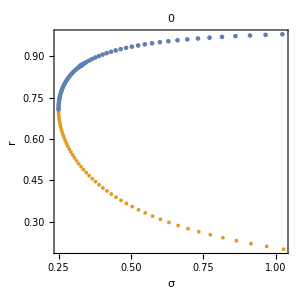
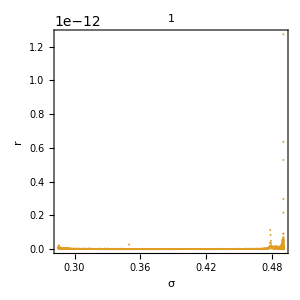
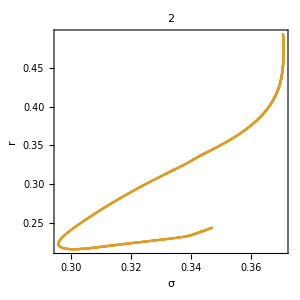
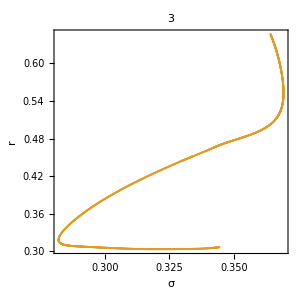
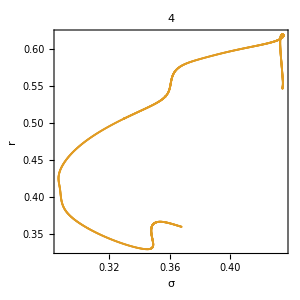
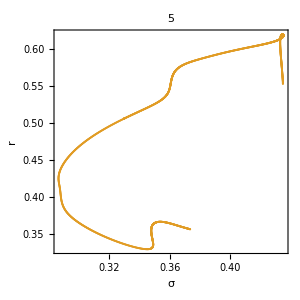
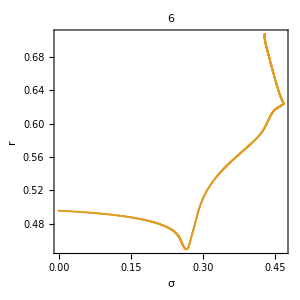
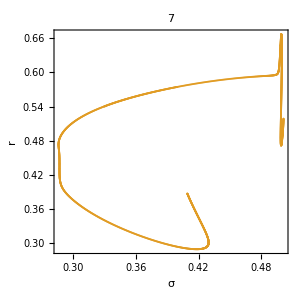

```mathematica
Show[ListPlot[branches[[#,All,{1,4}]],Joined->False,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[Dashed,ColorData[97,"ColorList"][[2]],AbsoluteThickness[1]]],ListPlot[stables[[#,All,{1,4}]],Joined->False,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2]]],PlotLabel->#-1,PlotRange->All]&/@inds
```

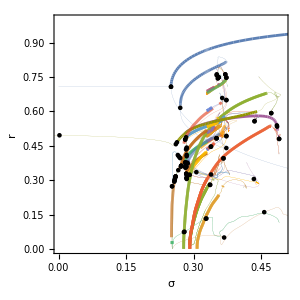

```mathematica
p=Show[Show[ListPlot[Transpose[{sigmas,orders}],PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.1]]],Graphics[{Table[Table[If[branches[[j,i,5]]<62&&Norm[{branches[[j,i,1]],Log[branches[[j,i,4]]]}-{branches[[j,i+1,1]],Log[branches[[j,i+1,4]]]}]>0,{AbsoluteThickness[0.1],ColorData[97,"ColorList"][[1+Mod[j-1,15]]],Line[{{branches[[j,i,1]],branches[[j,i,4]]},{branches[[j,i+1,1]],branches[[j,i+1,4]]}}]}],{i,1,Length[branches[[j]]]-1}],{j,1,Length[branches]}],Table[Table[If[branches[[j,i,5]]==62&&Norm[{branches[[j,i,1]],Log[branches[[j,i,4]]]}-{branches[[j,i+1,1]],Log[branches[[j,i+1,4]]]}]>0,{AbsoluteThickness[2],ColorData[97,"ColorList"][[1+Mod[j-1,15]]],Line[{{branches[[j,i,1]],branches[[j,i,4]]},{branches[[j,i+1,1]],branches[[j,i+1,4]]}}]}],{i,1,Length[branches[[j]]]-1}],{j,1,Length[branches]}]}]],ListPlot[DeleteCases[(Extract[#,Position[Differences[#[[All,5]]],u_/;Abs[u]>2]]&/@branches),{}][[All,All,{1,4}]],PlotStyle->Directive[Black]]]
```

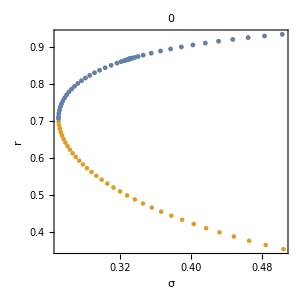
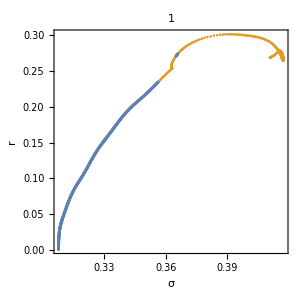
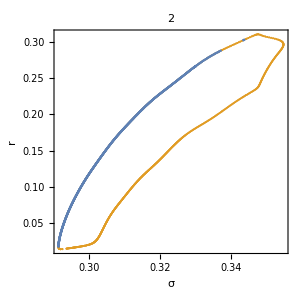
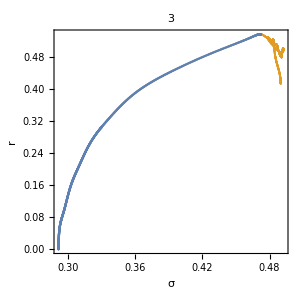
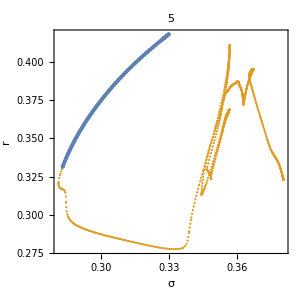
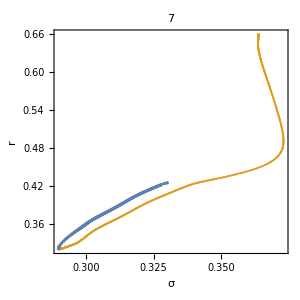
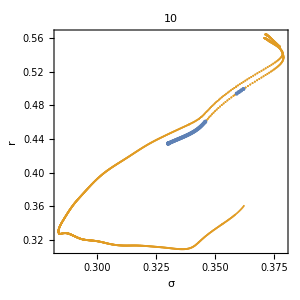
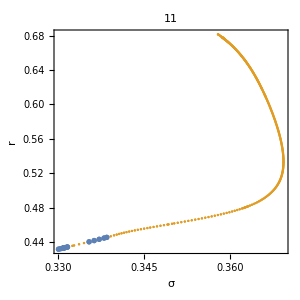

```mathematica
Show[ListPlot[branches[[#,All,{1,4}]],Joined->False,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[Dashed,ColorData[97,"ColorList"][[2]],AbsoluteThickness[1]]],ListPlot[stables[[#,All,{1,4}]],Joined->False,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2]]],PlotLabel->#-1,PlotRange->All]&/@inds
```

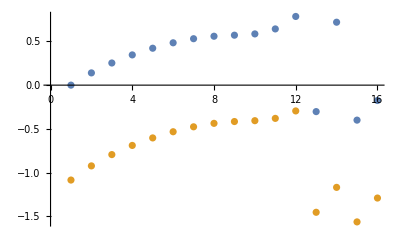

-Graphics- | -Graphics-

{1.,0.990199,0.968094,0.940781,0.912176,0.884959,0.862227,0.847577,0.841168,0.833124,0.800276,0.706937,0.954496,0.751946,0.920943,0.984582,0.,0.139662,0.250586,0.339015,0.409798,0.465669,0.506522,0.530672,0.540774,0.553086,0.599632,0.707277,-0.298225,0.659225,-0.389697,-0.174924,0.46626,0.602778,0.70062,0.771383,0.82315,0.861213,0.888479,0.905976,0.914566,0.918444,0.928559,0.956806,0.115943,0.390528,0.00626466,0.275605,-0.884648,-0.797909,-0.713534,-0.636371,-0.567824,-0.508244,-0.458918,-0.423328,-0.404436,-0.395551,-0.371186,-0.290728,-0.993256,-0.920591,-0.99998,-0.961271}

OutputStream[…]

OutputStream[…]

data/limitic.dat

```mathematica
dat=Partition[BinaryReadList["30.dat","Real64"],2501];
ind=1;
x=Catenate[{ConstantArray[1,{1,2501}],dat[[1;;15]]}];
y=Catenate[{ConstantArray[0,{1,2501}],dat[[16;;30]]}];
u=dat[[31;;46]];
v=dat[[47;;62]];
theta=ArcTan[x,y];
phi=ArcTan[u,v];
ListPlot[{theta[[All,ind]],phi[[All,ind]]}]

Grid[{{rasterizeBackground[ListDensityPlot[Transpose[theta],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[Transpose[phi],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]]}}]
ic=Catenate[{x[[All,1]],y[[All,1]],u[[All,1]],v[[All,1]]}]+0.0*RandomReal[{-1,1},64]
file=OpenWrite["data/limitic.dat",BinaryFormat->True]
BinaryWrite[file,ic,"Real64"]
Close[file]
```

### Steady solutions

```mathematica
sols=Solve[0==1+2*0.25*Sin[η]+0.33*Sin[η+2*Pi/16]+0.33*Sin[η+2*Pi/16],η]
thetas=Table[2*Pi/16*i,{i,1,15}];
phis=Table[η+2*Pi/16*i,{i,0,15}]/.sols[[1]];
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
Table[ToString[i]<>":"<>ToString[u[[i]]],{i,1,62}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{η→-2.29239},{η→-1.29676}}

{1:0.92388,2:0.707107,3:0.382683,4:0.,5:-0.382683,6:-0.707107,7:-0.92388,8:-1.,9:-0.92388,10:-0.707107,11:-0.382683,12:0.,13:0.382683,14:0.707107,15:0.92388,16:0.382683,17:0.707107,18:0.92388,19:1.,20:0.92388,21:0.707107,22:0.382683,23:0.,24:-0.382683,25:-0.707107,26:-0.92388,27:-1.,28:-0.92388,29:-0.707107,30:-0.382683,31:-0.660583,32:-0.322999,33:0.0637595,34:0.440811,35:0.750753,36:0.946399,37:0.997965,38:0.8976,39:0.660583,40:0.322999,41:-0.0637595,42:-0.440811,43:-0.750753,44:-0.946399,45:-0.997965,46:-0.8976,47:-0.750753,48:-0.946399,49:-0.997965,50:-0.8976,51:-0.660583,52:-0.322999,53:0.0637595,54:0.440811,55:0.750753,56:0.946399,57:0.997965,58:0.8976,59:0.660583,60:0.322999,61:-0.0637595,62:-0.440811}

```mathematica
sols=Solve[0==1+2*0.25*Sin[η]+2*0.33*Sin[η+4*Pi/16],η]
thetas=Table[4*Pi/16*i,{i,1,15}];
phis=Table[η+4*Pi/16*i,{i,0,15}]/.sols[[1]];
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
Table[ToString[i]<>":"<>ToString[u[[i]]],{i,1,62}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{η→-2.39263},{η→-1.6485}}

{1:0.707107,2:0.,3:-0.707107,4:-1.,5:-0.707107,6:0.,7:0.707107,8:1.,9:0.707107,10:0.,11:-0.707107,12:-1.,13:-0.707107,14:0.,15:0.707107,16:0.707107,17:1.,18:0.707107,19:0.,20:-0.707107,21:-1.,22:-0.707107,23:0.,24:0.707107,25:1.,26:0.707107,27:0.,28:-0.707107,29:-1.,30:-0.707107,31:-0.732398,32:-0.0364317,33:0.680876,34:0.999336,35:0.732398,36:0.0364317,37:-0.680876,38:-0.999336,39:-0.732398,40:-0.0364317,41:0.680876,42:0.999336,43:0.732398,44:0.0364317,45:-0.680876,46:-0.999336,47:-0.680876,48:-0.999336,49:-0.732398,50:-0.0364317,51:0.680876,52:0.999336,53:0.732398,54:0.0364317,55:-0.680876,56:-0.999336,57:-0.732398,58:-0.0364317,59:0.680876,60:0.999336,61:0.732398,62:0.0364317}

```mathematica
sols=Solve[{0==1+2*0.25*Sin[η1]+2*0.33*Sin[η+4*Pi/16]},{η,η2}]
```

```mathematica
Position[Import["auto/rel/twist.dat"],{}]
```

{{75},{996},{1572},{2456},{3410},{4548},{5035},{5640},{6037},{6890},{7070},{7111}}

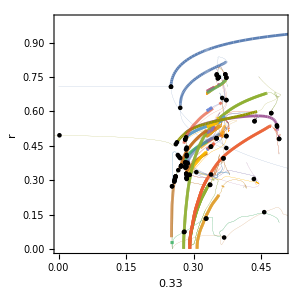

-Graphics-

```mathematica
steady=Join[{#[[1;;Position[#,{}][[1,1]]-1]]},Table[#[[Position[#,{}][[i,1]]+1;;Position[#,{}][[i+1,1]]-1]],{i,1,Length[Position[#,{}]]-1}]]&@Import["auto/rel/steady.dat"];
twist=Join[{#[[1;;Position[#,{}][[1,1]]-1]]},Table[#[[Position[#,{}][[i,1]]+1;;Position[#,{}][[i+1,1]]-1]],{i,1,Length[Position[#,{}]]-1}]]&@Import["auto/rel/twist.dat"];
twist2=Join[{#[[1;;Position[#,{}][[1,1]]-1]]},Table[#[[Position[#,{}][[i,1]]+1;;Position[#,{}][[i+1,1]]-1]],{i,1,Length[Position[#,{}]]-1}]]&@Import["auto/rel/twist2.dat"];
cluster=Join[{#[[1;;Position[#,{}][[1,1]]-1]]},Table[#[[Position[#,{}][[i,1]]+1;;Position[#,{}][[i+1,1]]-1]],{i,1,Length[Position[#,{}]]-1}]]&@Import["auto/rel/cluster.dat"];
cluster2=Join[{#[[1;;Position[#,{}][[1,1]]-1]]},Table[#[[Position[#,{}][[i,1]]+1;;Position[#,{}][[i+1,1]]-1]],{i,1,Length[Position[#,{}]]-1}]]&@Import["auto/rel/cluster2.dat"];
p
p2=ListPlot[Join[steady[[All,All,{1,4}]],twist[[All,All,{1,4}]],twist2[[All,All,{1,4}]],cluster[[All,All,{1,4}]],cluster2[[All,All,{1,4}]]],PlotRange->{{0,0.5},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]
```

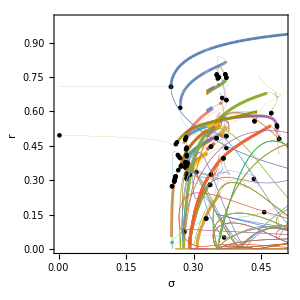

```mathematica
Show[p,p2]
```

-Graphics-

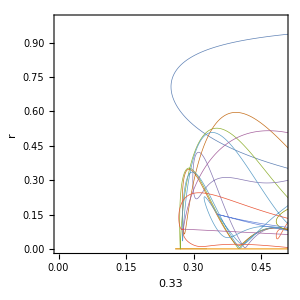

```mathematica
ListPlot[Join[steady[[All,All,{1,4}]],cluster2[[All,All,{1,4}]]],PlotRange->{{0,0.5},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]
ListPlot[Join[steady[[All,All,{1,4}]],twist[[All,All,{1,4}]]],PlotRange->{{0,0.5},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]
```

```mathematica
η=0;
σ=0.33;
β=0.25;
ω=1;
θ1=0;
SeedRandom[6];
sol=FindRoot[{0==ω/2+β*Sin[ϕ1]+σ*Sin[ϕ2+η],0==-ω/2+β*Sin[-ϕ1]+σ*Sin[θ2-ϕ1-η],0==ω/2+β*Sin[ϕ2-θ2]+σ*Sin[ϕ1-θ2+η]},{{θ2,RandomReal[]},{ϕ1,RandomReal[]},{ϕ2,RandomReal[]}}]
{ω/2+β*Sin[ϕ1-θ1]+σ*Sin[ϕ2-θ1+η],-ω/2+β*Sin[θ1-ϕ1]+σ*Sin[θ2-ϕ1-η],ω/2+β*Sin[ϕ2-θ2]+σ*Sin[ϕ1-θ2+η],-ω/2+β*Sin[θ2-ϕ2]+σ*Sin[θ1-ϕ2+η]}/.sol
thetas=Riffle[Table[θ2+η*i,{i,1,15,2}],Table[0+η*i,{i,2,15,2}]]/.sol;
phis=Riffle[Table[ϕ1+η*i,{i,0,15,2}],Table[ϕ2+η*i,{i,1,15,2}]]/.sol;
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,62}]
```

{θ2→-0.593873,ϕ1→-2.35928,ϕ2→-1.37618}

{3.87523×10^-13,-4.97297×10^-13,1.92263×10^-13,-8.25451×10^-14}

{1:0.828779,2:1.0,3:0.828779,4:1.0,5:0.828779,6:1.0,7:0.828779,8:1.0,9:0.828779,10:1.0,11:0.828779,12:1.0,13:0.828779,14:1.0,15:0.828779,16:-0.559575,17:0.0,18:-0.559575,19:0.0,20:-0.559575,21:0.0,22:-0.559575,23:0.0,24:-0.559575,25:0.0,26:-0.559575,27:0.0,28:-0.559575,29:0.0,30:-0.559575,31:-0.709288,32:0.193388,33:-0.709288,34:0.193388,35:-0.709288,36:0.193388,37:-0.709288,38:0.193388,39:-0.709288,40:0.193388,41:-0.709288,42:0.193388,43:-0.709288,44:0.193388,45:-0.709288,46:0.193388,47:-0.704919,48:-0.981122,49:-0.704919,50:-0.981122,51:-0.704919,52:-0.981122,53:-0.704919,54:-0.981122,55:-0.704919,56:-0.981122,57:-0.704919,58:-0.981122,59:-0.704919,60:-0.981122,61:-0.704919,62:-0.981122}

```mathematica
η=2*Pi/16;
σ=0.33;
β=0.25;
ω=1;
θ1=0;
SeedRandom[4];
sol=FindRoot[{0==ω/2+β*Sin[ϕ1]+σ*Sin[ϕ2+η],0==-ω/2+β*Sin[-ϕ1]+σ*Sin[θ2-ϕ1-η],0==ω/2+β*Sin[ϕ2-θ2]+σ*Sin[ϕ1-θ2+η]},{{θ2,RandomReal[]},{ϕ1,RandomReal[]},{ϕ2,RandomReal[]}}]
{ω/2+β*Sin[ϕ1-θ1]+σ*Sin[ϕ2-θ1+η],-ω/2+β*Sin[θ1-ϕ1]+σ*Sin[θ2-ϕ1-η],ω/2+β*Sin[ϕ2-θ2]+σ*Sin[ϕ1-θ2+η],-ω/2+β*Sin[θ2-ϕ2]+σ*Sin[θ1-ϕ2+η]}/.sol
thetas=Riffle[Table[θ2+η*i,{i,1,15,2}],Table[0+η*i,{i,2,15,2}]]/.sol;
phis=Riffle[Table[ϕ1+η*i,{i,0,15,2}],Table[ϕ2+η*i,{i,1,15,2}]]/.sol;
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,62}]
```

{θ2→-0.675365,ϕ1→-2.24616,ϕ2→-1.5708}

{-5.55112×10^-17,0.,5.55112×10^-17,0.}

{1:0.960315,2:0.707107,3:0.876269,4:0.0,5:0.278916,6:-0.707107,7:-0.481822,8:-1.0,9:-0.960315,10:-0.707107,11:-0.876269,12:0.0,13:-0.278916,14:0.707107,15:0.481822,16:-0.278916,17:0.707107,18:0.481822,19:1.0,20:0.960315,21:0.707107,22:0.876269,23:0.0,24:0.278916,25:-0.707107,26:-0.481822,27:-1.0,28:-0.960315,29:-0.707107,30:-0.876269,31:-0.625182,32:0.382683,33:0.109812,34:0.92388,35:0.780479,36:0.92388,37:0.993952,38:0.382683,39:0.625182,40:-0.382683,41:-0.109812,42:-0.92388,43:-0.780479,44:-0.92388,45:-0.993952,46:-0.382683,47:-0.780479,48:-0.92388,49:-0.993952,50:-0.382683,51:-0.625182,52:0.382683,53:0.109812,54:0.92388,55:0.780479,56:0.92388,57:0.993952,58:0.382683,59:0.625182,60:-0.382683,61:-0.109812,62:-0.92388}

```mathematica
M=10
η=2*Pi/M;
σ=0.33;
β=0.25;
ω=1;
θ1=0;
SeedRandom[2];
sol=FindRoot[{0==ω/2+β*Sin[ϕ1]+σ*Sin[ϕ2+η],0==-ω/2+β*Sin[-ϕ1]+σ*Sin[θ2-ϕ1-η],0==ω/2+β*Sin[ϕ2-θ2]+σ*Sin[ϕ1-θ2+η]},{{θ2,RandomReal[]},{ϕ1,RandomReal[]},{ϕ2,RandomReal[]}}]
{ω/2+β*Sin[ϕ1-θ1]+σ*Sin[ϕ2-θ1+η],-ω/2+β*Sin[θ1-ϕ1]+σ*Sin[θ2-ϕ1-η],ω/2+β*Sin[ϕ2-θ2]+σ*Sin[ϕ1-θ2+η],-ω/2+β*Sin[θ2-ϕ2]+σ*Sin[θ1-ϕ2+η]}/.sol
thetas=Riffle[Table[θ2+η*i,{i,1,M-1,2}],Table[0+η*i,{i,2,M-1,2}]]/.sol;
phis=Riffle[Table[ϕ1+η*i,{i,0,M-1,2}],Table[ϕ2+η*i,{i,1,M-1,2}]]/.sol;
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]
```

10

{θ2→-12.5664,ϕ1→-14.0579,ϕ2→-14.0579}

{5.55112×10^-16,-4.44089×10^-16,2.22045×10^-16,0.0307071}

{1:0.809017,2:0.309017,3:-0.309017,4:-0.809017,5:-1.0,6:-0.809017,7:-0.309017,8:0.309017,9:0.809017,10:0.587785,11:0.951057,12:0.951057,13:0.587785,14:-0.00000000000000569646,15:-0.587785,16:-0.951057,17:-0.951057,18:-0.587785,19:0.0791545,20:0.649978,21:0.972533,22:0.923612,23:0.521904,24:-0.0791545,25:-0.649978,26:-0.972533,27:-0.923612,28:-0.521904,29:-0.996862,30:-0.759953,31:-0.232767,32:0.383328,33:0.853004,34:0.996862,35:0.759953,36:0.232767,37:-0.383328,38:-0.853004}

```mathematica
M=10
η=0;
σ=0.33;
β=0.25;
ω=1;
θ1=0;
SeedRandom[6];
sol=FindRoot[{0==ω/2+β*Sin[ϕ1]+σ*Sin[ϕ2+η],0==-ω/2+β*Sin[-ϕ1]+σ*Sin[θ2-ϕ1-η],0==ω/2+β*Sin[ϕ2-θ2]+σ*Sin[ϕ1-θ2+η]},{{θ2,RandomReal[]},{ϕ1,RandomReal[]},{ϕ2,RandomReal[]}}]
{ω/2+β*Sin[ϕ1-θ1]+σ*Sin[ϕ2-θ1+η],-ω/2+β*Sin[θ1-ϕ1]+σ*Sin[θ2-ϕ1-η],ω/2+β*Sin[ϕ2-θ2]+σ*Sin[ϕ1-θ2+η],-ω/2+β*Sin[θ2-ϕ2]+σ*Sin[θ1-ϕ2+η]}/.sol
thetas=Riffle[Table[θ2+η*i,{i,1,M-1,2}],Table[0+η*i,{i,2,M-1,2}]]/.sol;
phis=Riffle[Table[ϕ1+η*i,{i,0,M-1,2}],Table[ϕ2+η*i,{i,1,M-1,2}]]/.sol;
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]
```

10

{θ2→-0.593873,ϕ1→-2.35928,ϕ2→-1.37618}

{3.87523×10^-13,-4.97297×10^-13,1.92263×10^-13,-8.25451×10^-14}

{1:0.828779,2:1.0,3:0.828779,4:1.0,5:0.828779,6:1.0,7:0.828779,8:1.0,9:0.828779,10:-0.559575,11:0.0,12:-0.559575,13:0.0,14:-0.559575,15:0.0,16:-0.559575,17:0.0,18:-0.559575,19:-0.709288,20:0.193388,21:-0.709288,22:0.193388,23:-0.709288,24:0.193388,25:-0.709288,26:0.193388,27:-0.709288,28:0.193388,29:-0.704919,30:-0.981122,31:-0.704919,32:-0.981122,33:-0.704919,34:-0.981122,35:-0.704919,36:-0.981122,37:-0.704919,38:-0.981122}

```mathematica
M=10
η=2*Pi/M;
σ=0.33;
β=0.25;
ω=1;
θ1=0;
SeedRandom[1];
sol=FindRoot[{0==ω/2+β*Sin[ϕ1]+σ*Sin[ϕ2+η],0==-ω/2+β*Sin[-ϕ1]+σ*Sin[θ2-ϕ1-η],0==ω/2+β*Sin[ϕ2-θ2]+σ*Sin[ϕ1-θ2+η]},{{θ2,RandomReal[]},{ϕ1,RandomReal[]},{ϕ2,RandomReal[]}}]
{ω/2+β*Sin[ϕ1-θ1]+σ*Sin[ϕ2-θ1+η],-ω/2+β*Sin[θ1-ϕ1]+σ*Sin[θ2-ϕ1-η],ω/2+β*Sin[ϕ2-θ2]+σ*Sin[ϕ1-θ2+η],-ω/2+β*Sin[θ2-ϕ2]+σ*Sin[θ1-ϕ2+η]}/.sol
thetas=Riffle[Table[θ2+η*i,{i,1,M-1,2}],Table[0+η*i,{i,2,M-1,2}]]/.sol;
phis=Riffle[Table[ϕ1+η*i,{i,0,M-1,2}],Table[ϕ2+η*i,{i,1,M-1,2}]]/.sol;
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]
```

10

{θ2→-0.445814,ϕ1→-2.19911,ϕ2→-2.64493}

{5.55112×10^-17,5.55112×10^-17,0.,-0.341067}

{1:0.983392,2:0.309017,3:0.131275,4:-0.809017,5:-0.90226,6:-0.809017,7:-0.688902,8:0.309017,9:0.476495,10:0.181493,11:0.951057,12:0.991346,13:0.587785,14:0.431193,15:-0.587785,16:-0.724854,17:-0.951057,18:-0.879177,19:-0.587785,20:-0.431193,21:0.587785,22:0.724854,23:0.951057,24:0.879177,25:0.0000000000000000612323,26:-0.181493,27:-0.951057,28:-0.991346,29:-0.809017,30:-0.90226,31:-0.809017,32:-0.688902,33:0.309017,34:0.476495,35:1.0,36:0.983392,37:0.309017,38:0.131275}